```mathematica
(* Define vertices of our triangle *)
triangle={
{0.0,0.0},
{1.0,0.0},
{0.5,Sqrt[3]/2}
};

(* Define vertices of tetrahedron *)
tetrahedron={
{0.0, 0.0,           0.0},
{2.0, 0.0,           0.0},
{1.0, Sqrt[3], 0.0},
{1.0, Sqrt[3]/2, Sqrt[3]}
};

(* Functions for converting back and forth from cartesian to barycentric *)
ComputeBarycentric[v_, simplex_:triangle]:=With[
{ mat=Append[Transpose[simplex],ConstantArray[1,Dimensions[simplex][[1]] ]] },
LinearSolve[mat,Append[v,1]]
]
ComputeCartesian[v_, simplex_:triangle] := v . simplex

(* Functions to plot functions of 3-rankings on the triangle (2-simplex) *)
ContourPlotTriangle[f_] := 
ContourPlot[ 
f[ComputeBarycentric[{x,y}]], 
{x,0,1},{y,0,1},
PlotLegends -> Automatic,
PlotPoints -> 5,
Contours -> 20,
ContourStyle-> None,
RegionFunction-> Function[
{x,y}, {x,y}∈Triangle[triangle]  ]
]
DensityPlotTriangle[f_] := 
DensityPlot[ 
f[ComputeBarycentric[{x,y}]], 
{x,y}∈Triangle[triangle],
PlotLegends -> Automatic,
PlotPoints->100
]
Plot3DTriangle[f_] := 
Plot3D[ 
f[ComputeBarycentric[{x,y}]], 
{x,0,1},{y,0,1},
PlotLegends -> Automatic,
PlotPoints -> 5,
RegionFunction-> Function[
{x,y}, {x,y}∈Triangle[triangle]  ]
]
(* Functions to plot functions of 4-rankings on the tetrahedron (3-simplex) *)
DensityTetrahedron[f_]:=
DensityPlot3D[
f[ComputeBarycentric[{x,y,z}, tetrahedron]],
{x,y,z}∈DiscretizeRegion[Tetrahedron[tetrahedron]],
ColorFunction->ColorData["M10DefaultDensityGradient","ColorFunction"],
Boxed->False,
Axes->False,
PlotPoints->50
]
SphericalPlotTetrahedron[f_]:=
SliceDensityPlot3D[
Module[{c},
c=ComputeCartesian[ConstantArray[1/4,4], tetrahedron];
f[ComputeBarycentric[c+({x,y,z}/8), tetrahedron]]
],
"CenterSphere",{x,-2,2},{y,-2,2},{z,-2,2},
ColorFunction->ColorData["M10DefaultDensityGradient","ColorFunction"],
Boxed->False,
Axes->False,
PlotPoints->100
]


(* Function to plot a correlation metric by computing it relative to some 'root3_' point. *)
RelativePlotDensity[f_, root3_]:= DensityPlotTriangle[f[#, root3]&]
RelativePlot3D[f_, root3_]:= Plot3DTriangle[f[#, root3]&]
RelativePlot3DC[f_, root4_]:= ContourPlotTetrahedron[f[#, root4]&]
RelativePlotS[f_, root4_]:= SphericalPlotTetrahedron[f[#, root4]&]
RelativePlotT[f_, root4_]:= DensityTetrahedron[f[#, root4]&]

root3 = {0.7, 0.25, 0.05};
(*root4 = {4/10, 3/10, 2/10,1/10};*)
root4 = {0.6, 0.3, 0.075, 0.025};

(* Function to show a plot togehter with permutations of a 'root3_' point. *)
ShowWithRootPermutations[plot_, root3_] :=
Show[
plot,
ListPlot[ ComputeCartesian /@ Complement[Permutations[root3],{root3}], PlotStyle->Green ],
ListPlot[ ComputeCartesian /@ {root3}, PlotStyle->Red ]
]

ShowWithRootPermutations4[graphic_, root4_, df_:Identity] :=
Module[{transform},
c = ComputeCartesian[ConstantArray[1/4,4], tetrahedron];
transform[p_] := 2Normalize[p-c];
Show[
graphic,
ListPointPlot3D[ transform /@ (ComputeCartesian[#,tetrahedron]& /@ Complement[Permutations[root4],{root4}]), PlotStyle->Green ],
ListPointPlot3D[ transform /@ (ComputeCartesian[#,tetrahedron]& /@ {root4}), PlotStyle->Red ],
DisplayFunction -> df
]
]

MyLabel[tolabel_, text_]:=Labeled[
tolabel,text, Top, LabelStyle->{FontSize -> Large}]

(* An inverse of the softmax only exists up to a constant, but because we only *)
SoftmaxInverse[p_, c_]:=Log[#]+c&/@p
```

```mathematica
ShannonEntropy[p_]:=-Sum[Log[p[[i]]]*p[[i]],{i,1,Length[p]}]
```

```mathematica
(*ContourPlotTetrahedron[ShannonEntropy]*)
```

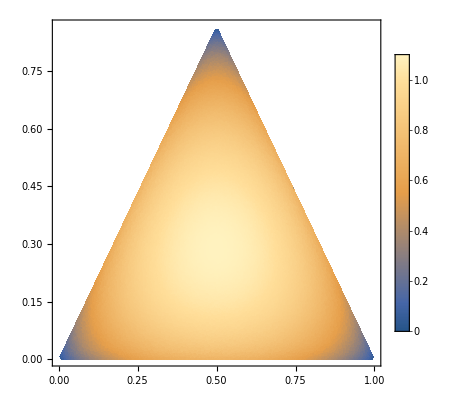
-Graphics-Shannon Entropy

```mathematica
MyLabel[DensityPlotTriangle[ShannonEntropy],"Shannon Entropy"]
(*Show[DensityTetrahedron[ShannonEntropy]]*)
```

```mathematica
(*ShowWithRootPermutations4[RelativePlotS[KendallTau,root4],root4]
Export["C:\\Users\\stefa\\Desktop\\test.obj",%]
*)
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[KendallTau, root3], root3],"Kendall Tau"],
ShowWithRootPermutations4[RelativePlotS[KendallTau,root4],root4]
},Spacer[10]],ImageSizeMultipliers->1]
```

KendallTau::rctneqln: The arguments to KendallTau are not a pair of vectors or matrices of equal length.

```mathematica
-Graphics3D-
-Graphics3D-
```

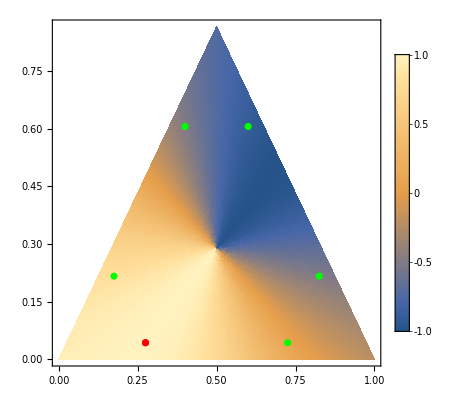
-Graphics-Pearson Correlation

```mathematica
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[Correlation, root3], root3],"Pearson Correlation"],
ShowWithRootPermutations4[RelativePlotS[Correlation,root4],root4]
},Spacer[10]],ImageSizeMultipliers->1]
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

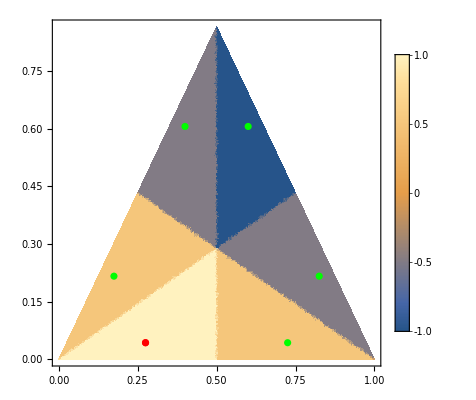
-Graphics-Spearman Rho

```mathematica
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[SpearmanRho, root3], root3],"Spearman Rho"],
ShowWithRootPermutations4[RelativePlotS[SpearmanRho,root4],root4]
},Spacer[10]],ImageSizeMultipliers->1]
```

```mathematica
(*graphic = RelativePlot3DC[KendallTau, root4]
Export["tetrahedron_kendall_tau.3ds",graphic]*)
```

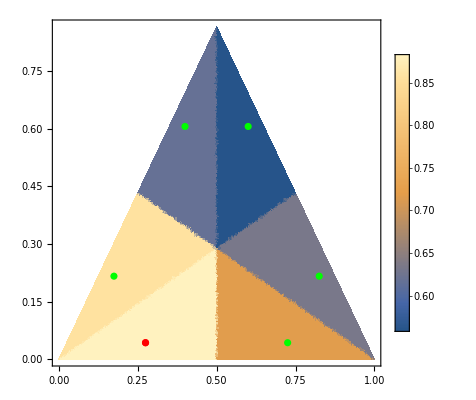
-Graphics-DCG

```mathematica
(* Discounted Cumulative Gain *)
DCGp[p_,a_,rel_]/;Length[a]==Length[rel]:=Module[
{c=Sort[ Transpose[{rel,a}], #1[[2]]>#2[[2]]& ]},
Sum[c[[i,1]]/Log2[i+1],{i,1,p}] ]

DCG[a_,rel_] := DCGp[Length[rel],a,rel]

Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[DCG, root3], root3],"DCG"],
(*ShowWithRootPermutations4[RelativePlotS[DCG,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```

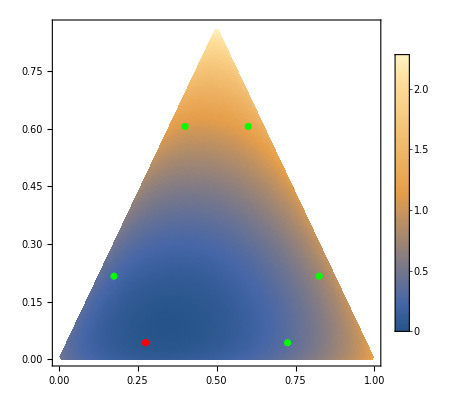
-Graphics-XE_NDCG

```mathematica
XENDCG[p_,q_,gamma_, c_]:=Module[{qnew,qold},
qold=SoftmaxInverse[q,c];
qnew = Normalize[((2^#)& /@ qold)-gamma,Norm[#,1]&];
KLDivergence[p, qnew]
]
XENDCG2[p_,q_]:=XENDCG[p, q, {0,0,0},0]

Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[XENDCG2, root3], root3],"XE_NDCG"],
(*ShowWithRootPermutations4[RelativePlotS[RR1,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```

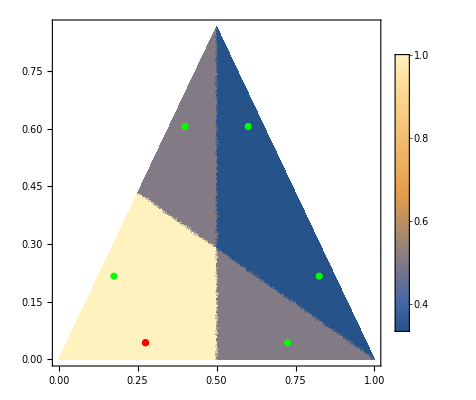
-Graphics-Reciprocal Rank

```mathematica
(* Reciprocal Rank *)
RRp[p_,a_,rel_]/;Length[a]==Length[rel]:=Module[
{b,brel},
brel = MemberQ[TakeLargest[rel,p],#]& /@ rel;
b=Transpose[Sort[ Transpose[{brel,a}], #1[[2]]>#2[[2]]& ]][[1]];
1/FirstPosition[b,True]
]
RR1[a_,rel_]:=RRp[1,a,rel]
RR2[a_,rel_]:=RRp[2,a,rel]

Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[RR1, root3], root3],"Reciprocal Rank"],
(*ShowWithRootPermutations4[RelativePlotS[RR1,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```

```mathematica
(*R[g_,i_]:=(2^g[[i]]-1)/(2^Max[g]-1)*)
ERR[a_,rel_]:=
Block[
{p=1,err=0,r, g},
g=Transpose[
ReverseSortBy[ Transpose[{rel,a}], #[[2]]&,NumericalOrder ]
][[1]];
Do[
r=g[[i]];(*R[g,i];*)
err=err+(p*r)/i;
p=p*(1-r);,
{i,1,Length[g]}
]; err
]
(*ERR[a_,rel_]/; Length[a]==Length[rel],Total[a]==1:=Module[
{n, g},
n=Length[a];
g=Reverse[Transpose[SortBy[ Transpose[{rel,a}], #[[2]]&,NumericalOrder ]][[1]] ] ;
Print[g];
Sum[
(1/r)*Product[
(1-g[[i]])*g[[r]],
{i,1,r-1}
],
{r,1,n}]]*)
```

```mathematica
(*ERR[{3/6,2/6,1/6},{2/6,3/6,1/6}]
ERR[{4/10,3/10,2/10,1/10},{3/10,4/10,1/10,2/10}]*)
```

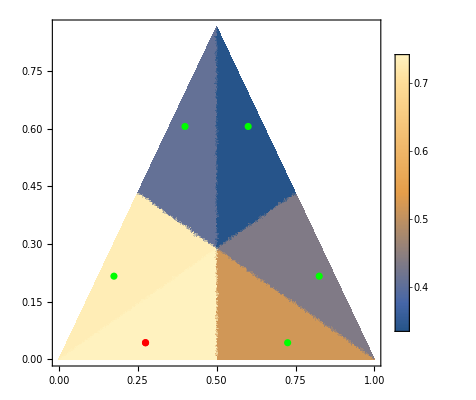

```mathematica
Style[Row[{
ShowWithRootPermutations[RelativePlotDensity[ERR, root3], root3],
(*ShowWithRootPermutations4[RelativePlotS[ERR,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```

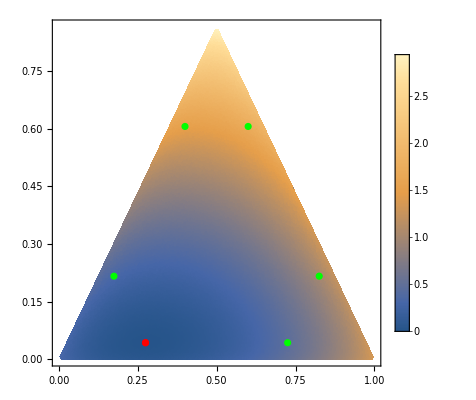
-Graphics-KL Divergence

```mathematica
KLDivergence[p_, q_]/; Length[p] == Length[q]:=Sum[ p[[k]]*Log[p[[k]]/q[[k]]],{k,1,Length[p]} ]
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[KLDivergence, root3], root3],"KL Divergence"],
(*ShowWithRootPermutations4[RelativePlotS[KLDivergence,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]

corner = {0.99,0.009,0.001};
(*ShowWithRootPermutations[RelativePlotDensity[KLDivergence, corner], corner]*)
```

```mathematica
CrossEntropy[p_,q_]/; Length[p] == Length[q]:=-Sum[ p[[k]]*Log[q[[k]]],{k,1,Length[p]} ]
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[CrossEntropy, root3], root3],"Cross Entropy"],
ShowWithRootPermutations4[RelativePlotS[KLDivergence,root4],root4]
},Spacer[10]],ImageSizeMultipliers->1]
```

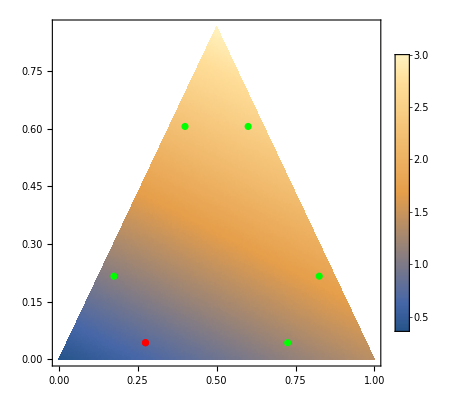
```mathematica
-Graphics-"Cross Entropy"
```

-Graphics-Cross Entropy

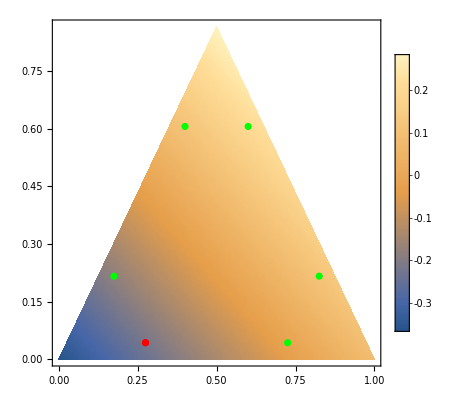
-Graphics-Barycentric Dot

```mathematica
SoftPlus[x_,beta_:1]:=1/beta*Log[1+Exp[beta*x]]
BaryDot[a_,b_] /;Length[a]==Length[b]:= Module[{n,aa,bb},
n = Length[a];
aa = a-ConstantArray[1/n,n];
bb = b-ConstantArray[1/n,n];
(*SoftPlus[-(aa.bb)+ Norm[bb]^2, 25] *)
-(aa.bb)
]
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[BaryDot, root3], root3],"Barycentric Dot"],
(*ShowWithRootPermutations4[RelativePlotS[BaryDot,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```

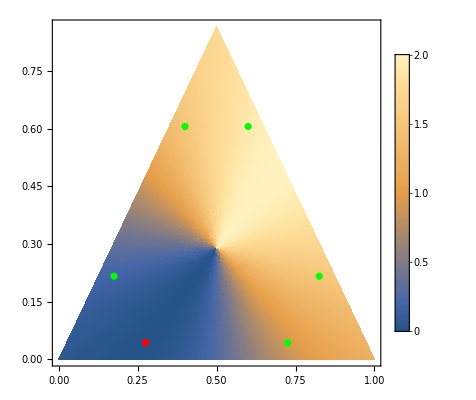
-Graphics-Barycentric Cos

```mathematica
BaryCos[a_,b_] /;Length[a]==Length[b]:= Module[{n,aa,bb},
n = Length[a];
aa = a-ConstantArray[1/n,n];
bb = b-ConstantArray[1/n,n];
CosineDistance[aa,bb]
(*+SoftPlus[0.5-Total[Abs[aa]],25]*)
]
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[BaryCos, root3], root3],"Barycentric Cos"],
(*ShowWithRootPermutations4[RelativePlotS[BaryCos,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```

```mathematica
BaryAngle[a_,b_] /;Length[a]==Length[b]:= Module[{n,aa,bb},
n = Length[a];
aa = a-ConstantArray[1/n,n];
bb = b-ConstantArray[1/n,n];
(VectorAngle[aa,bb])]
Style[Row[{
ShowWithRootPermutations[RelativePlotDensity[BaryAngle, root3], root3],
(*ShowWithRootPermutations4[RelativePlotS[BaryAngle,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```

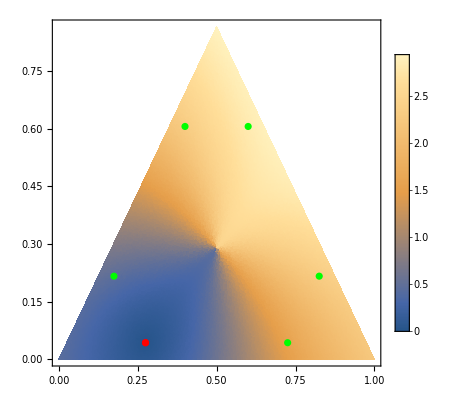
-Graphics-Barycentric Cos+Norm

```mathematica
BaryCombo[a_, b_]:= BaryCos[a,b] + Norm[a-b]
Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[BaryCombo, root3], root3],"Barycentric Cos+Norm"],
(*MyLabel[ShowWithRootPermutations[RelativePlotDensity[BaryCombo, corner], corner],"Barycentric Dot+Norm (b)"]*)
(*ShowWithRootPermutations4[RelativePlotS[BaryCombo,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
(*Show[RelativePlot3D[BaryCombo, root3]]*)
```

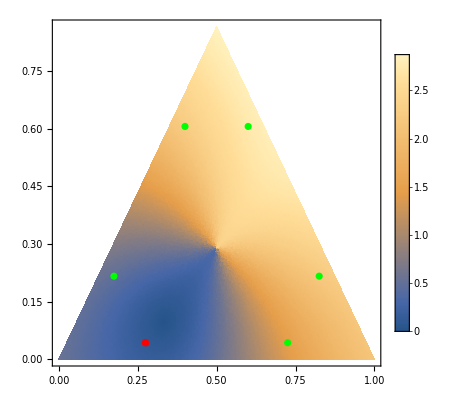
-Graphics-Barycentric Dot+Norm+Middle

```mathematica
ConstructIdeal[p_]:=Module[{values},
n=Length[p];
values=Sum[Join[ConstantArray[0,i],ConstantArray[1/(n-i),n-i]],{i,0,n-1}]/n;
values=SortBy[Transpose[{p,values}],#[[1]]& ];
Transpose[values][[2]]
]

Test[p_,q_]/;Length[a]==Length[b]:= Module[{ideal,n,a,b,c},
ideal=ConstructIdeal[q];
n = Length[p];
a = p-ConstantArray[1/n,n];
b = q - ConstantArray[1/n,n];
c = ideal-ConstantArray[1/n,n];
CosineDistance[a,c]+Norm[a-c](*Norm[a-1.5c]^(2/3)*)
]

Style[Row[{
MyLabel[ShowWithRootPermutations[RelativePlotDensity[Test, root3], root3],"Barycentric Dot+Norm+Middle"],
(*MyLabel[ShowWithRootPermutations[RelativePlotDensity[BaryCombo, corner], corner],"Barycentric Dot+Norm (b)"]*)
(*ShowWithRootPermutations4[RelativePlotS[BaryCombo,root4],root4]*)
},Spacer[10]],ImageSizeMultipliers->1]
```